```mathematica
VertexDegreeEnumeration[v_]:=VertexDegreeEnumeration[1,Length[v],v];
VertexDegreeEnumeration[i_,n_,v_]:=Join@@(Function[S,Join[i<->#&/@#,S]]/@
VertexDegreeEnumeration[i+1,n,ReplacePart[v,Prepend[#->v[[#]]-1&/@#,i->0]]]&/@
Subsets[Select[Range[i+1,n],v[[#]]>0&],{v[[i]]}]);
VertexDegreeEnumeration[n_,n_,v_]:=If[v[[n]]==0,{{}},{}];
```

List the cubic graphs of size 6.

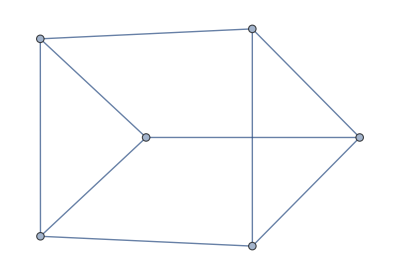
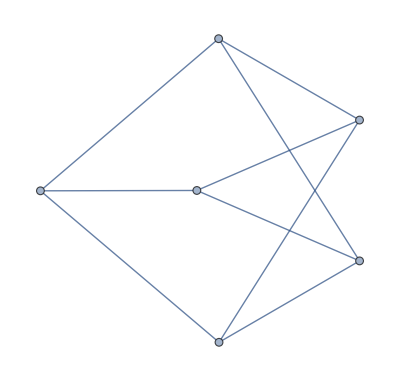

```mathematica
DeleteDuplicates[Graph/@VertexDegreeEnumeration[3&/@Range[6]],IsomorphicGraphQ]
```